```mathematica
(* code to make list of edges for piece of square grid *)
makesqlatticeedges[xx_,yy_]:=(* yy better be even? *) Module[{index=0,bondlist=Table[Null,{2xx*yy-xx-yy}],numbonds=0,nextbondlist=Table[Null,{(xx-1)*(yy-1)}],numnextbonds=0},
Do[
index++;
If[n>1,
numbonds++;
bondlist[[numbonds]]={index,index-1};
];
If[m>1,
numbonds++;
bondlist[[numbonds]]={index,index-yy};
];
If[(m>1)&&(n>1),
numnextbonds++;
nextbondlist[[numnextbonds]]={index,index-yy-1};
];
,{m,xx},{n,yy}];
bondlist=bondlist[[1;;numbonds]];
nextbondlist=nextbondlist[[1;;numnextbonds]];
{bondlist,nextbondlist}
];

(* coordinates of vertices, with SW corner at {1,1} *)
makesqlattice11[xx_,yy_]:=(* yy better be even? *) Flatten[Table[{m,n},{m,1,xx},{n,1,yy}],1];

(* generate edges oriented randomly towards or away from origin *)
makedirectedp[posn_,edge_,p_]:=Module[{L=Length[edge],p1,p2,tog},
Table[p1=posn[[edge[[i,1]]]];p2=posn[[edge[[i,2]]]];tog=1;
If[p>RandomReal[],tog=tog*-1];
If[Total[Abs[p1]]<Total[Abs[p2]],tog=tog*-1];
If[tog>0,edge[[i,1]]->edge[[i,2]],edge[[i,2]]->edge[[i,1]]],
{i,L}]]

(* indices of vertices at the boundary *)
boundaryverts[L_]:=Module[{LL=2L+1},Join[Range[LL],Range[LL+1,LL^2,LL],Range[2LL,LL^2-2L,LL],Range[LL^2-2L+1,LL^2-1]]]

(* edges that connect all boundary vertices to a "point at infinity" *)
wireboundary[L_]:=Module[{bv=boundaryverts[L]},Table[bv[[i]]->(2L+1)^2+1,{i,Length[bv]}]]
```

```mathematica
(* Run this cell to initialize grid size and edge data *)
L=4;
LL=2L+1;
grid=Flatten[Table[{i,j},{i,-L,L},{j,-L,L}],1];
pos=makesqlattice11[LL,LL];
edge=makesqlatticeedges[LL,LL][[1]];
cent=2 L^2+2L+1;
outer=LL^2+1;
```

```mathematica
(* plot with mathematica's graph drawing *)
p=0.3;
g=makedirectedp[grid,edge,p];
gg=Graph[g,VertexCoordinates->grid];
HighlightGraph[gg,{2 L^2+2L+1,1}]
HighlightGraph[gg,PathGraph[FindShortestPath[gg,2 L^2+2L+1,1]]]
```

-Graphics-

-Graphics-

```mathematica
(* generate data, 1000 configurations at each probability p *)
data41=Table[
{p,
Table[
g=makedirectedp[grid,edge,p];
gg=Graph[g,VertexCoordinates->grid];
g2=Join[g,wireboundary[L]];
vc=VertexOutComponent[gg,{cent}];
{GraphDistance[Graph[g2],cent,outer],
vc}
,{i,1000}]},{p,0,1,.02}];
```

```mathematica
(* created a very large file! 250 megabytes *)
Save["data41",data41]
```

```mathematica
(* functions to extract various things from data *)
ExtractPercProb[data_]:=Table[{data[[i,1]],(1000-Count[data[[i,2,All,1]],Infinity])/1000},{i,Length[data]}]

ExtractVCSize[data_]:=Table[{data[[i,1]],Mean[Table[Length[data[[i,2,j,2]]],{j,1000}]]},{i,Length[data]}]

MakeAveragePic[data_,L_]:=Module[{vc},
Table[Sum[vc=data[[i,2,j,2]];
SparseArray[Table[pos[[vc[[i]]]]->1,{i,Length[vc]}],{2L+1,2L+1}],{j,1000}]
,{i,Length[data]}]
]
```

```mathematica
avpics=MakeAveragePic[data41,L];
```

```mathematica
Save["avpics41",avpics]
```

```mathematica
Manipulate[Image[Normal[avpics[[j]]]/1000.],{j,1,Length[avpics],1}]
```

```mathematica
Export["avpics41.gif",Table[Image[Normal[avpics[[j]]]/1000.],{j,Length[avpics]}]]
```

avpics41.gif

```mathematica
meanvcs41=ExtractVCSize[data41];
```

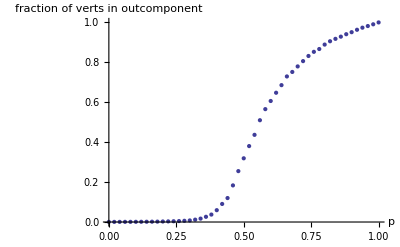

```mathematica
ListPlot[Transpose[Transpose[meanvcs41]*{1,1/(outer-1)}],AxesLabel->{"p","fraction of verts in outcomponent"}]
```

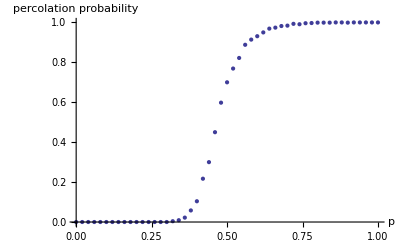

```mathematica
ListPlot[ExtractPercProb[data41],AxesLabel->{"p","percolation probability"}]
```

```mathematica
Timing[p=0.6;
g=makedirectedp[grid,edge,p];
Length[VertexOutComponent[Graph[g],{481}]]]
```

{0.050701,566}

```mathematica
DrawPic[vc_,pos_,L_,c_:False]:=Module[{imtab},imtab=SparseArray[Table[If[c&&vc[[i]]==2L^2+2L+1,pos[[vc[[i]]]]->2,pos[[vc[[i]]]]->1],{i,Length[vc]}],{2L+1,2L+1}];
Colorize[Normal[imtab]]]
```

```mathematica
(* make bitmap pictures just of the out component *)
p=.7;
Table[
g=makedirectedp[grid,edge,p];
gg=Graph[g,VertexCoordinates->grid];
(*HighlightGraph[gg,{Subgraph[gg,VertexOutComponent[gg,{2 L^2+2L+1}]],Labeled[2 L^2+2L+1,2 L^2+2L+1]}]*)
vc=VertexOutComponent[gg,{2 L^2+2L+1}];
{p,DrawPic[vc,pos,L,True]},{p,{0.1,0.3,0.45,0.49,0.51,0.55,0.7,0.9}}]
```

{{0.1,-Graphics-},{0.3,-Graphics-},{0.45,-Graphics-},{0.49,-Graphics-},{0.51,-Graphics-},{0.55,-Graphics-},{0.7,-Graphics-},{0.9,-Graphics-}}

```mathematica
(* picture of shortest path to boundary *)
Timing[
g2=Join[g,wireboundary[L]];
sp=FindShortestPath[Graph[g2],2 L^2+2L+1,(2L+1)^2+1];
{Length[sp],If[Length[sp]>0,DrawPic[sp[[1;;-2]],pos,L],Null]}]
```

{0.004525,{31,-Graphics-}}